# Лабораторная работа №2 Моделирование непрерывной случайной величины

```mathematica
dir=NotebookDirectory[];
```

```mathematica
paramsMM=Import[dir<>"inputMM.txt","List"]
```

{1159453,220760,961853,14039333,3219,2698,571,24273,100}

```mathematica
file=dir<>"outputDiscrDistrib.txt";
```

```mathematica
LCG[a_,c_,M_,x_]:=Mod[a x+c,M]
```

```mathematica
GenerateRSwithLCG[a_,c_,M_,x0_,n_]:=Module[{outputSeq=Table[0,{j,1,n}],i},
outputSeq⟦1⟧=LCG[a,c,M,x0];
For[i=2,i≤n,i++,outputSeq⟦i⟧=LCG[a,c,M,outputSeq⟦i-1⟧]];
Return[N[outputSeq/M,10]]
]
```

```mathematica
MMG[paramList1_,paramList2_,n_,K_]:=Module[{α=Table[0,{i,1,n}],b,c,s,t,V},
b=GenerateRSwithLCG[paramList1⟦2⟧,paramList1⟦3⟧,paramList1⟦4⟧,paramList1⟦1⟧,n+K];
c=GenerateRSwithLCG[paramList2⟦2⟧,paramList2⟦3⟧,paramList2⟦4⟧,paramList2⟦1⟧,n+K];
V=b⟦1;;K⟧;
For[t=1,t≤n,t++,s=IntegerPart[c⟦t⟧K];α⟦t⟧=V⟦s+1⟧;V⟦s+1⟧=b⟦t+K⟧];
Return[α]
]
```

```mathematica
n=10^5
```

100000

```mathematica
MyPearsonChiSquareTest[sample_,k_,dist_,ϵ_]:=Module[{cells,h,H,i, n=Length[sample],ni=0,pi,Xleft=0,Xright,
sortSample=Sort[sample],pos=1,Xmin,Xmax,χ2 =0,Δ=InverseCDF[ChiSquareDistribution[k-1],1-ϵ]},
Xmin=sortSample⟦1⟧;Xmax=sortSample⟦n⟧;h=(Xmax-Xmin)/k; Xright=Xmin+h;pi=CDF[dist,N[Xright]];
For[i=1,i<k,i++,While[sortSample⟦pos⟧<Xright,ni++;pos++] ; χ2+=(ni-n pi)^2/(n pi);ni=0; Xleft=Xright;Xright+=h;
pi=CDF[dist,N[Xright]]-CDF[dist,N[Xleft]]];
Xleft=Xmax-h;pi=1-CDF[dist,N[Xleft]];pos=n;
While[sortSample⟦pos⟧>Xleft,ni++;pos--];χ2+=(ni-n pi)^2/(n pi) ;
H=If[χ2<Δ,0,1]; Return[{H,N[χ2],Δ}]
 ]
```

```mathematica
K=1000;ϵ=0.05;ΔK=1.36;
```

```mathematica
MyKolmogorovTest[sample_,n_,dist_,Δ_]:=Module[{D,difference,i,H,Fe=Table[(i-1)/n,{i,1,n}],k=1,left,S,sortSample=Sort[sample]},
D=Max[Abs[Fe-CDF[dist,sortSample]]]; S=√n D;
H=Boole[S≥Δ]; Return[{H,S,Δ}]]
```

```mathematica
sampleMM=MMG[paramsMM⟦1;;4⟧,paramsMM⟦5;;8⟧,n ,paramsMM⟦9⟧];
```

## Моделирование НСВ с равномерным распределением

```mathematica
UniformCRVGenerator[sample_,a_,b_]:=InverseCDF[UniformDistribution[{a,b}],sample]
```

```mathematica
a=-1;b=1;
```

### Моделироваие на основе генератора Макларена-Марсальи

```mathematica
uniformSampleForMM=UniformCRVGenerator[sampleMM,a,b];
```

```mathematica
mean1=Mean[UniformDistribution[{a,b}]];smean1MM=Mean[uniformSampleForMM];Print[{mean1,smean1MM}]
```

{0,-0.00085821}

```mathematica
variance1=Variance[UniformDistribution[{a,b}]];svariance1MM=Variance[uniformSampleForMM];Print[{variance1, svariance1MM}]
```

{1/3,0.333050558}

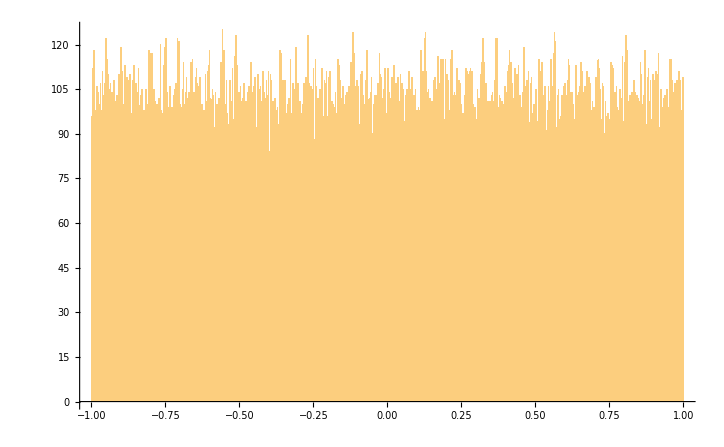

```mathematica
Histogram[uniformSampleForMM,1000]
```

```mathematica
MPCSTres1ForMM=MyPearsonChiSquareTest[uniformSampleForMM,K,UniformDistribution[{a,b}],ϵ]
```

{0,805.129,1073.64}

```mathematica
MKTres1ForMM=MyKolmogorovTest[uniformSampleForMM,n,UniformDistribution[{a,b}],ΔK]
```

{0,0.3984186,1.36}

### Моделирование на основе встроенного программного генератора

```mathematica
uniformSampleForInline=UniformCRVGenerator[RandomReal[1,n],a,b];
```

```mathematica
smean1Inline=Mean[uniformSampleForInline];Print[{mean1,smean1Inline}]
```

{0,-0.000134915}

```mathematica
svariance1Inline=Variance[uniformSampleForInline];Print[{variance1, svariance1Inline}]
```

{1/3,0.334187}

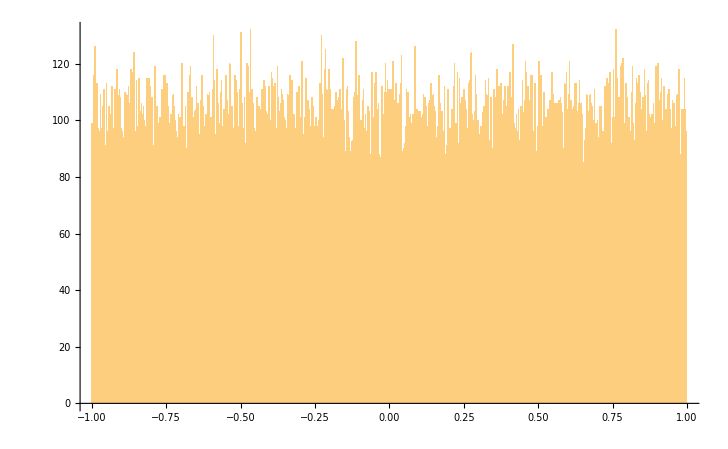

```mathematica
Histogram[uniformSampleForInline,1000]
```

```mathematica
MPCSTres1ForInline=MyPearsonChiSquareTest[uniformSampleForInline,K,UniformDistribution[{a,b}],ϵ]
```

{0,1067.82,1073.64}

```mathematica
MKTres1ForInline=MyKolmogorovTest[uniformSampleForInline,n,UniformDistribution[{a,b}],ΔK]
```

{0,0.604829,1.36}

## Моделирование ДСВ с нормальным распределением

```mathematica
NormalCRVGenerator[sample_,n_,μ_,σ_]:=Module[{i,resSample=Table[0,{i,1,n}]},
For[i=0,i<n,i++,resSample⟦i+1⟧=σ(-6+∑_(j=1)^12 (sample⟦12i+j⟧))+μ];
Return[resSample]]
```

```mathematica
μ=0;σ=1/5;
```

### Моделирование на основе генератора Макларена-Марсальи

```mathematica
normalSampleForMM=NormalCRVGenerator[MMG[paramsMM⟦1;;4⟧,paramsMM⟦5;;8⟧,12n ,paramsMM⟦9⟧],n,μ,σ];
```

```mathematica
mean2=Mean[NormalDistribution[μ,σ]];smean2MM=Mean[normalSampleForMM];Print[{mean2,smean2MM}]
```

{0,0.000064563}

```mathematica
variance2=Variance[NormalDistribution[μ,σ]];svariance2MM=Variance[normalSampleForMM];Print[{variance2, svariance2MM}]
```

{1/25,0.039878544}

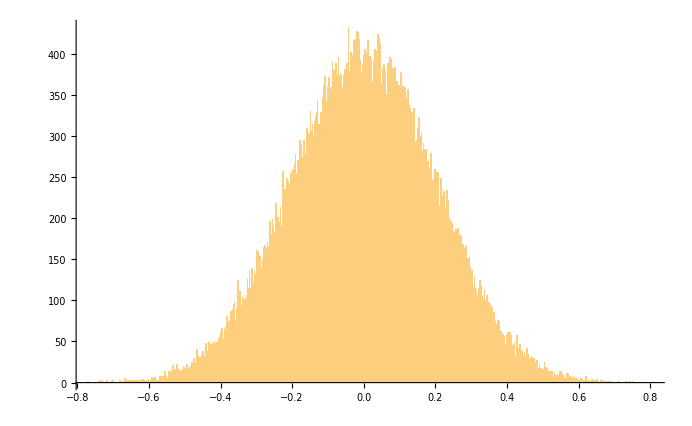

```mathematica
Histogram[normalSampleForMM,1000]
```

```mathematica
MPCSTres2ForMM=MyPearsonChiSquareTest[normalSampleForMM,K,NormalDistribution[μ,σ],ϵ]
```

{0,957.251,1073.64}

```mathematica
MKTres2ForMM=MyKolmogorovTest[normalSampleForMM,n,NormalDistribution[μ,σ],ΔK]
```

{0,1.1579,1.36}

### Моделирование на основе встроенного программного генератора

```mathematica
normalSampleForInline=NormalCRVGenerator[RandomReal[1,12 n],n,μ,σ];
```

```mathematica
smean2Inline=Mean[normalSampleForInline];Print[{mean2,smean2Inline}]
```

{0,-0.000273605}

```mathematica
svariance2Inline=Variance[normalSampleForInline];Print[{variance2, svariance2Inline}]
```

{1/25,0.0396568}

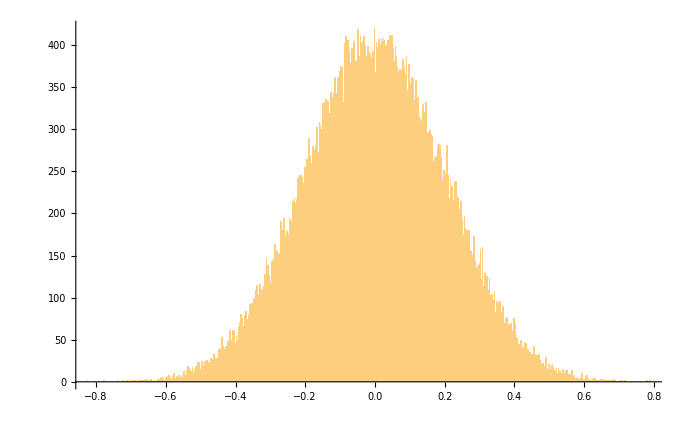

```mathematica
Histogram[normalSampleForInline,1000]
```

```mathematica
MPCSTres2ForInline=MyPearsonChiSquareTest[normalSampleForInline,K,NormalDistribution[μ,σ],ϵ]
```

{0,971.625,1073.64}

```mathematica
MKTres2ForInline=MyKolmogorovTest[normalSampleForInline,n,NormalDistribution[μ,σ],ΔK]
```

{0,0.862334,1.36}

## Моделирование НСВ с логнормальным распределением

```mathematica
LogNormalCRVGenerator[sample_,n_,μ_,σ_]:=Exp[NormalCRVGenerator[sample, n,μ, σ]]
```

### Моделирование на основе генератора Макларена - Марсальи

```mathematica
logNormalSampleForMM=LogNormalCRVGenerator[MMG[paramsMM⟦1;;4⟧,paramsMM⟦5;;8⟧,12n ,paramsMM⟦9⟧],n,μ,σ];
```

```mathematica
mean3=Mean[LogNormalDistribution[μ,σ]];smean3MM=Mean[logNormalSampleForMM];Print[{N[mean3],smean3MM}]
```

{1.0202,1.02019976}

```mathematica
variance3=Variance[LogNormalDistribution[μ,σ]];svariance3MM=Variance[logNormalSampleForMM];Print[{N[variance3], svariance3MM}]
```

{0.0424763,0.042235883}

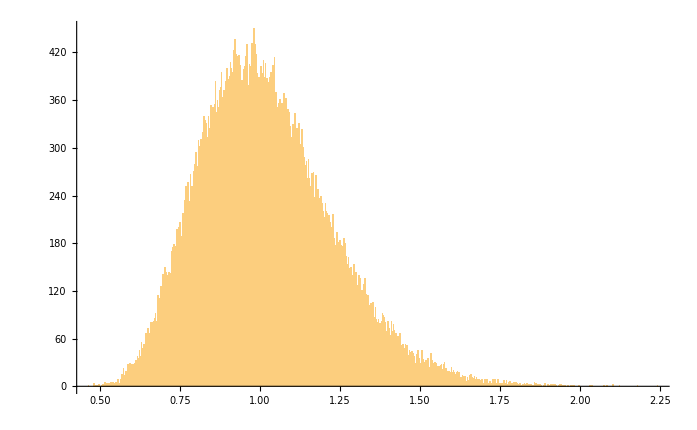

```mathematica
Histogram[logNormalSampleForMM,1000]
```

```mathematica
MPCSTres3ForMM=MyPearsonChiSquareTest[logNormalSampleForMM,K,LogNormalDistribution[μ, σ],ϵ]
```

{0,940.248,1073.64}

```mathematica
MKTres3ForMM=MyKolmogorovTest[logNormalSampleForMM,n,LogNormalDistribution[μ, σ],ΔK]
```

{0,1.1579,1.36}

### Моделирование на основе встроенного программного генератора

```mathematica
logNormalSampleForInline=LogNormalCRVGenerator[RandomReal[1, 12n],n,μ,σ];
```

```mathematica
smean3Inline=Mean[logNormalSampleForInline];Print[{N[mean3],smean3Inline}]
```

{1.0202,1.0189}

```mathematica
svariance3Inline=Variance[logNormalSampleForInline];Print[{N[variance3], svariance3Inline}]
```

{0.0424763,0.0419798}

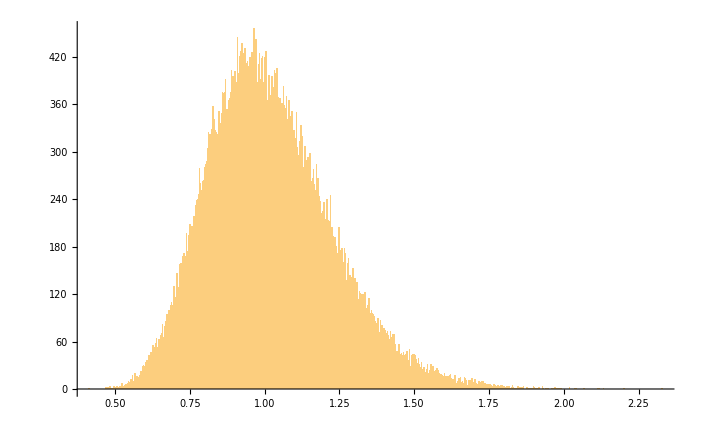

```mathematica
Histogram[logNormalSampleForInline,1000]
```

```mathematica
MPCSTres3ForInline=MyPearsonChiSquareTest[logNormalSampleForInline,K,LogNormalDistribution[μ,σ],ϵ]
```

{0,834.577,1073.64}

```mathematica
MKTres3ForInline=MyKolmogorovTest[logNormalSampleForInline,n,LogNormalDistribution[μ,σ],ΔK]
```

{1,1.38592,1.36}

## Моделирование НСВ с показательным распределением

```mathematica
ExponentialCRVGenerator[sample_,λ_]:=(-Log[sample])/λ
```

```mathematica
λ=2;
```

### Моделирование на основе генератора Макларена-Марсальи

```mathematica
exponentialSampleForMM=ExponentialCRVGenerator[sampleMM,λ];
```

```mathematica
mean4=Mean[ExponentialDistribution[λ]];smean4MM=Mean[exponentialSampleForMM];Print[{N[mean4],smean4MM}]
```

{0.5,0.5008698651}

```mathematica
variance4=Variance[ExponentialDistribution[λ]];svariance4MM=Variance[exponentialSampleForMM];Print[{N[variance4], svariance4MM}]
```

{0.25,0.251268755}

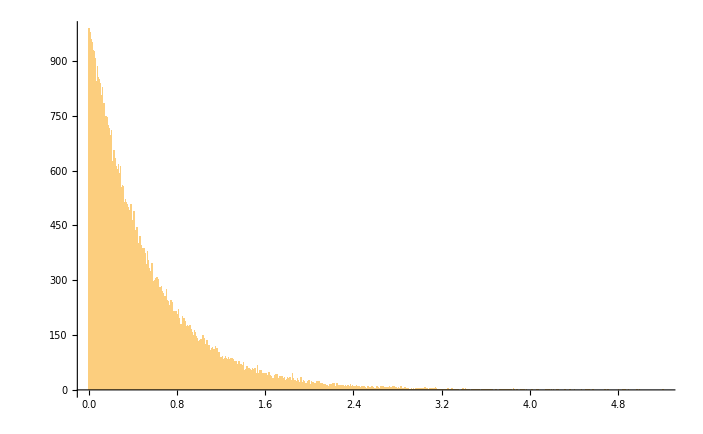

```mathematica
Histogram[exponentialSampleForMM,1000]
```

```mathematica
MPCSTres4ForMM=MyPearsonChiSquareTest[exponentialSampleForMM,K,ExponentialDistribution[λ],ϵ]
```

{0,1022.09,1073.64}

```mathematica
MKTres4ForMM=MyKolmogorovTest[exponentialSampleForMM,n,ExponentialDistribution[λ],ΔK]
```

{0,0.4015809,1.36}

### Моделирование на основе встроенного программного генератора

```mathematica
exponentialSampleForInline=ExponentialCRVGenerator[RandomReal[1,n],λ];
```

```mathematica
smean4Inline=Mean[exponentialSampleForInline];Print[{N[mean4],smean4Inline}]
```

{0.5,0.498673}

```mathematica
svariance4Inline=Variance[exponentialSampleForInline];Print[{N[variance4], svariance4Inline}]
```

{0.25,0.248778}

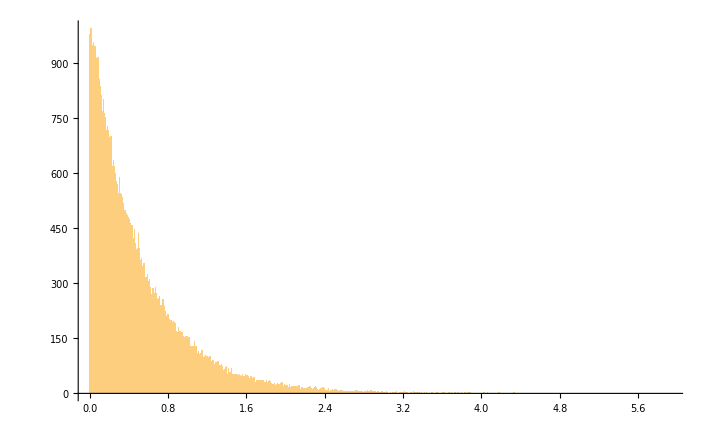

```mathematica
Histogram[exponentialSampleForInline,1000]
```

```mathematica
MPCSTres4ForInline=MyPearsonChiSquareTest[exponentialSampleForInline,K,ExponentialDistribution[λ],ϵ]
```

{0,936.843,1073.64}

```mathematica
MKTres4ForInline=MyKolmogorovTest[exponentialSampleForInline,n,ExponentialDistribution[λ],ΔK]
```

{0,1.0957,1.36}

## Моделирование НСВ с логистическим распределением

```mathematica
LogisticCRVGenerator[sample_,n_,a_,b_]:=a+b Log[sample/(1-sample)]
```

```mathematica
a=2;b=3;
```

### Моделирование на основе генератора Макларена - Марсальи

```mathematica
logisticSampleForMM=LogisticCRVGenerator[sampleMM,n,a,b];
```

```mathematica
mean5=Mean[LogisticDistribution[a,b]];smean5MM=Mean[logisticSampleForMM];Print[{N[mean5],smean5MM}]
```

{2.,1.9900626}

```mathematica
variance5=Variance[LogisticDistribution[a,b]];svariance5MM=Variance[logisticSampleForMM];Print[{N[variance5], svariance5MM}]
```

{29.6088,29.667298}

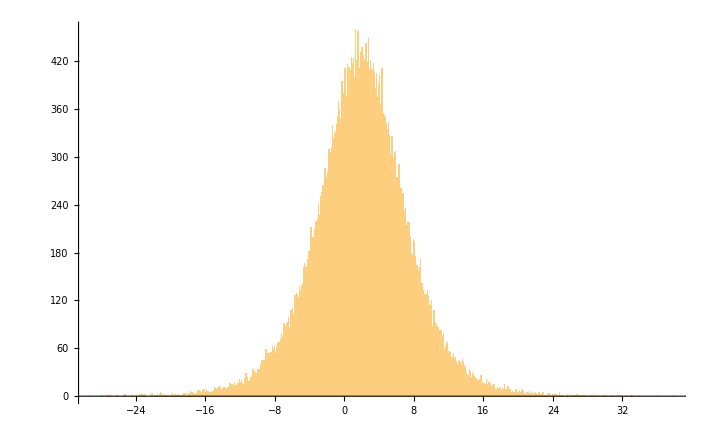

```mathematica
Histogram[logisticSampleForMM,1000]
```

```mathematica
MPCSTres5ForMM=MyPearsonChiSquareTest[logisticSampleForMM,K,LogisticDistribution[a,b],ϵ]
```

{0,966.455,1073.64}

```mathematica
MKTres5ForMM=MyKolmogorovTest[logisticSampleForMM,n,LogisticDistribution[a,b],ΔK]
```

{0,0.3984186,1.36}

### Моделирование на основе встроенного программного генератора

```mathematica
logisticSampleForInline=LogisticCRVGenerator[RandomReal[1,n],n,a,b];
```

```mathematica
smean5Inline=Mean[logisticSampleForInline];Print[{N[mean5],smean5Inline}]
```

{2.,1.9927}

```mathematica
svariance5Inline=Variance[logisticSampleForInline];Print[{N[variance5], svariance5Inline}]
```

{29.6088,29.6139}

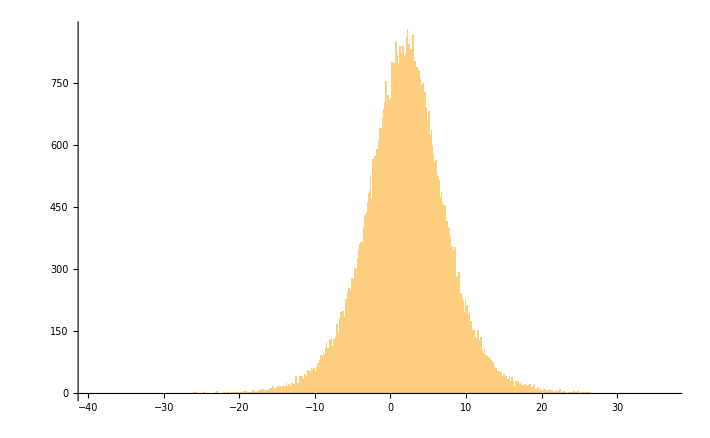

```mathematica
Histogram[logisticSampleForInline,1000]
```

```mathematica
MPCSTres5ForInline=MyPearsonChiSquareTest[logisticSampleForInline,K,LogisticDistribution[a,b],ϵ]
```

{0,942.408,1073.64}

```mathematica
MKTres5ForInline=MyKolmogorovTest[logisticSampleForInline,n,LogisticDistribution[a,b],ΔK]
```

{0,0.876636,1.36}

## Моделирование НСВ с распределением Вейбулла-Гнеденко

```mathematica
WGCRVGenerator[sample_,k_,λ_]:=InverseCDF[WeibullDistribution[k,λ],sample]
```

```mathematica
k=2;λ=5;
```

### Моделирование на основе генератора Макларена - Марсальи

```mathematica
WGSampleForMM=WGCRVGenerator[sampleMM,k,λ];
```

```mathematica
mean6=Mean[WeibullDistribution[k,λ]];smean6MM=Mean[WGSampleForMM];Print[{N[mean6],smean6MM}]
```

{4.43113,4.4271835}

```mathematica
variance6=Variance[WeibullDistribution[k,λ]];svariance6MM=Variance[WGSampleForMM];Print[{N[variance6], svariance6MM}]
```

{5.36505,5.3607813}

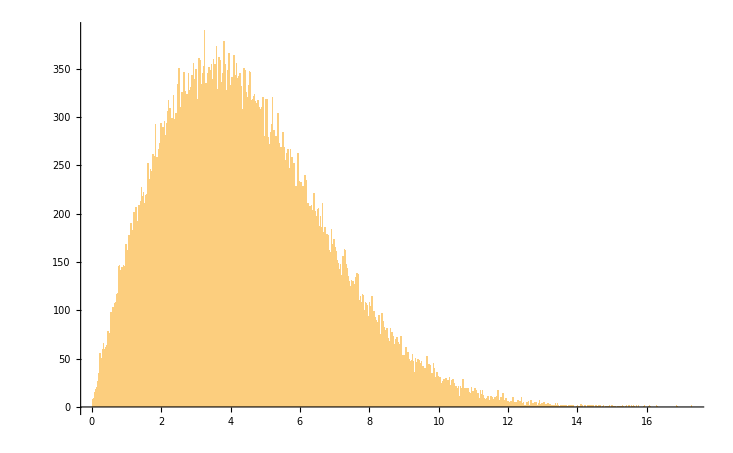

```mathematica
Histogram[WGSampleForMM,1000]
```

```mathematica
MPCSTres6ForMM=MyPearsonChiSquareTest[WGSampleForMM,K,WeibullDistribution[k,λ],ϵ]
```

{0,920.905,1073.64}

```mathematica
MKTres6ForMM=MyKolmogorovTest[WGSampleForMM,n,WeibullDistribution[k,λ],ΔK]
```

{0,0.3984186,1.36}

### Моделирование на основе встроенного программного генератора

```mathematica
WGSampleForInline=WGCRVGenerator[RandomReal[1,n],k,λ];
```

```mathematica
smean6Inline=Mean[WGSampleForInline];Print[{N[mean6],smean6Inline}]
```

{4.43113,4.44216}

```mathematica
svariance6Inline=Variance[WGSampleForInline];Print[{N[variance6], svariance6Inline}]
```

{5.36505,5.40359}

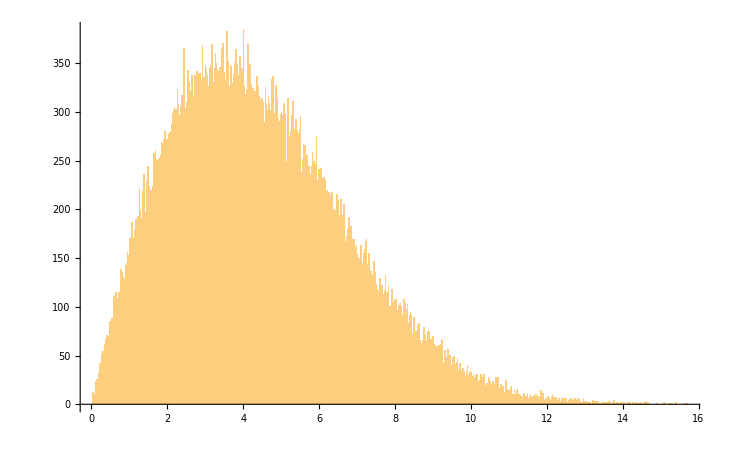

```mathematica
Histogram[WGSampleForInline,1000]
```

```mathematica
MPCSTres6ForInline=MyPearsonChiSquareTest[WGSampleForInline,K,WeibullDistribution[k,λ],ϵ]
```

{0,1033.21,1073.64}

```mathematica
MKTres6ForInline=MyKolmogorovTest[WGSampleForInline,n,WeibullDistribution[k,λ],ΔK]
```

{0,1.35812,1.36}

## Моделирование НСВ с гамма-распределением

```mathematica
GammaCRVGenerator[sample_,n_,α_,β_]:=Module[{expSample=ExponentialCRVGenerator[sample,1/β],i,resSample=Table[0,{i,1,n}]},
For[i=0,i<n,i++,resSample⟦i+1⟧=∑_(j=1)^α expSample⟦α i+j⟧]; Return[resSample]]
```

```mathematica
α=6;β=2;
```

### Моделирование на основе генератора Макларена - Марсальи

```mathematica
gammaSampleForMM=GammaCRVGenerator[MMG[paramsMM⟦1;;4⟧,paramsMM⟦5;;8⟧,α n ,paramsMM⟦9⟧],n,α,β];
```

```mathematica
mean7=Mean[GammaDistribution[α,β]];smean7MM=Mean[gammaSampleForMM];Print[{N[mean7],smean7MM}]
```

{12.,11.9987051}

```mathematica
variance7=Variance[GammaDistribution[α,β]];svariance7MM=Variance[gammaSampleForMM];Print[{N[variance7], svariance7MM}]
```

{24.,23.9176037}

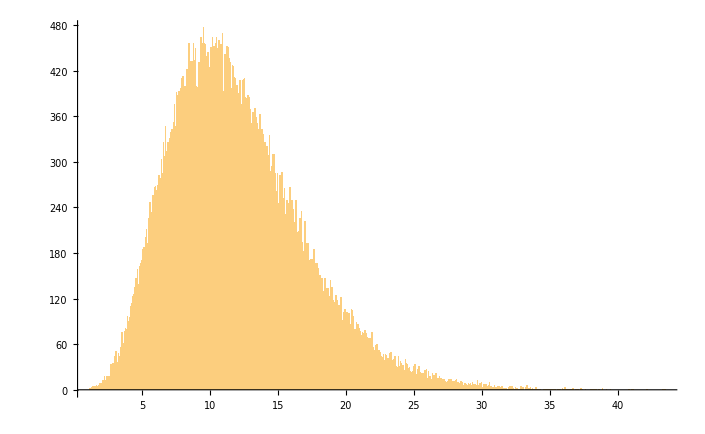

```mathematica
Histogram[gammaSampleForMM,1000]
```

```mathematica
MPCSTres7ForMM=MyPearsonChiSquareTest[gammaSampleForMM,K,GammaDistribution[α,β],ϵ]
```

{0,944.309,1073.64}

```mathematica
MKTres7ForMM=MyKolmogorovTest[gammaSampleForMM,n,GammaDistribution[α,β],ΔK]
```

{0,0.484048,1.36}

### Моделирование на основе встроенного программного генератора

```mathematica
gammaSampleForInline=GammaCRVGenerator[RandomReal[1,α n],n,α,β];
```

```mathematica
smean7Inline=Mean[gammaSampleForInline];Print[{N[mean7],smean7Inline}]
```

{12.,12.0059}

```mathematica
svariance7Inline=Variance[gammaSampleForInline];Print[{N[variance7], svariance7Inline}]
```

{24.,23.9544}

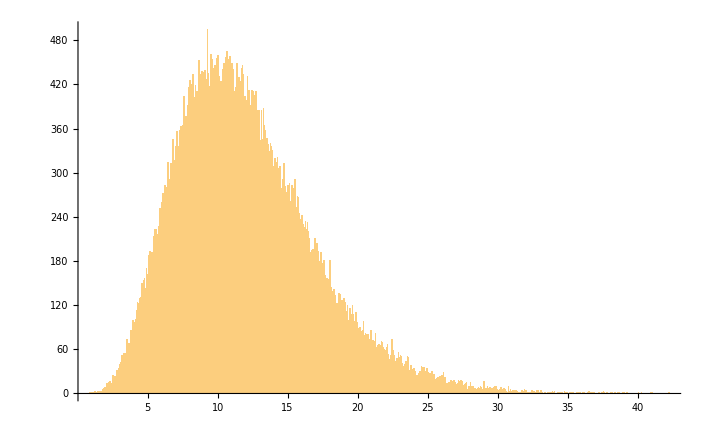

```mathematica
Histogram[gammaSampleForInline,1000]
```

```mathematica
MPCSTres7ForInline=MyPearsonChiSquareTest[gammaSampleForInline,K,GammaDistribution[α,β],ϵ]
```

{0,1071.12,1073.64}

```mathematica
MKTres7ForInline=MyKolmogorovTest[gammaSampleForInline,n,GammaDistribution[α,β],ΔK]
```

{0,0.813699,1.36}

## Моделирование НСВ с распределением Коши

```mathematica
CauchyCRVGenerator[sample_,n_,m_,c_]:=InverseCDF[CauchyDistribution[m,c],sample]
```

```mathematica
m=3;c=2.5;
```

### Моделирование на основе генератора Макларена - Марсальи

```mathematica
cauchySampleForMM=CauchyCRVGenerator[sampleMM,n,m,c];
```

```mathematica
mean8=Mean[CauchyDistribution[m,c]];smean8MM=Mean[cauchySampleForMM];Print[{N[mean8],smean8MM}]
```

{Indeterminate,5.60659}

```mathematica
variance8=Variance[CauchyDistribution[m,c]];svariance8MM=Variance[cauchySampleForMM];Print[{N[variance8], svariance8MM}]
```

{Indeterminate,283271.}

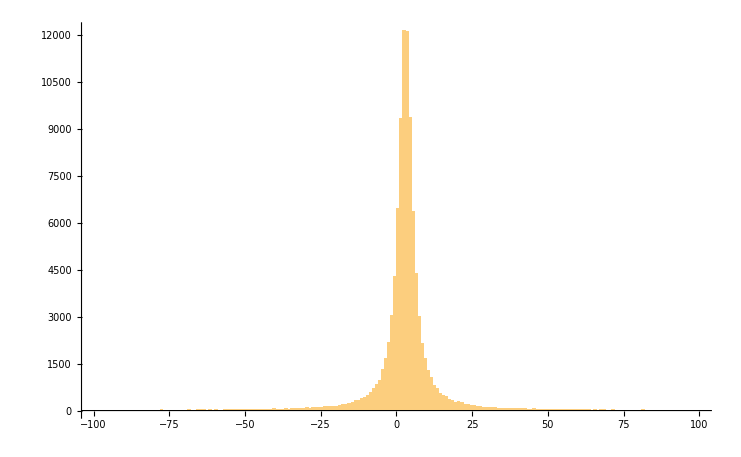

```mathematica
Histogram[cauchySampleForMM,{-100,100,1}]
```

```mathematica
MPCSTres8ForMM=MyPearsonChiSquareTest[cauchySampleForMM,K,CauchyDistribution[m,c],ϵ]
```

{0,992.203,1073.64}

```mathematica
MKTres8ForMM=MyKolmogorovTest[cauchySampleForMM,n,CauchyDistribution[m,c],ΔK]
```

{0,0.398419,1.36}

### Моделирование на основе встроенного программного генератора

```mathematica
cauchySampleForInline=CauchyCRVGenerator[RandomReal[1,n],n,m,c];
```

```mathematica
smean8Inline=Mean[cauchySampleForInline];Print[{N[mean8],smean8Inline}]
```

{Indeterminate,1.49369}

```mathematica
svariance8Inline=Variance[cauchySampleForInline];Print[{N[variance8], svariance8Inline}]
```

{Indeterminate,98982.9}

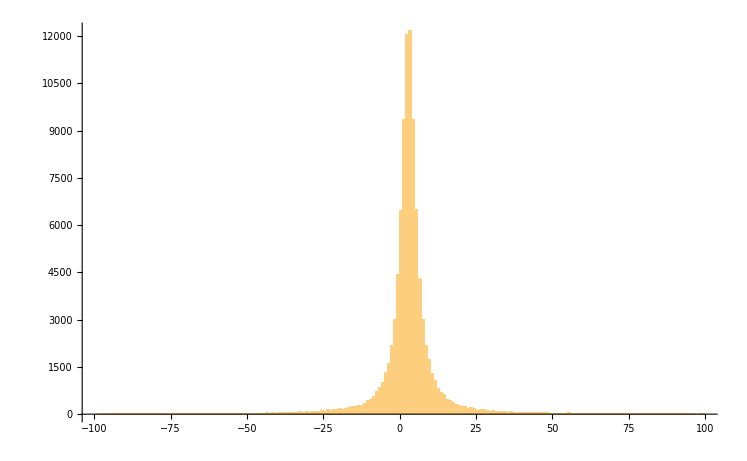

```mathematica
Histogram[cauchySampleForInline, {-100,100,1}]
```

```mathematica
MPCSTres8ForInline=MyPearsonChiSquareTest[cauchySampleForInline,K,CauchyDistribution[m,c],ϵ]
```

{0,520.514,1073.64}

```mathematica
MKTres8ForInline=MyKolmogorovTest[cauchySampleForInline,n,CauchyDistribution[m,c],ΔK]
```

{0,0.624879,1.36}

## Моделирование НСВ с распределением Стьюдента

```mathematica
StudentCRVGenerator[sample_,n_,m_]:=Module[{Y=Table[{NormalCRVGenerator[sample⟦12 i n+1;;12 (i+1)n⟧,n,0,1]},{i,0,m}]},
Return[Flatten[Y⟦1⟧/(√(1/m∑_(j=2)^(m+1) (Y⟦j⟧)^2))]]]
```

```mathematica
m=7;
```

### Моделирование на основе генератора Макларена - Марсальи

```mathematica
studentSampleForMM=StudentCRVGenerator[MMG[paramsMM⟦1;;4⟧,paramsMM⟦5;;8⟧,12(m+1)n ,paramsMM⟦9⟧],n,m];
```

```mathematica
mean9=Mean[StudentTDistribution[m]];smean9MM=Mean[studentSampleForMM];Print[{N[mean9],smean9MM}]
```

{0.,0.0014886}

```mathematica
variance9=Variance[StudentTDistribution[m]];svariance9MM=Variance[studentSampleForMM];Print[{N[variance9], svariance9MM}]
```

{1.4,1.3749328}

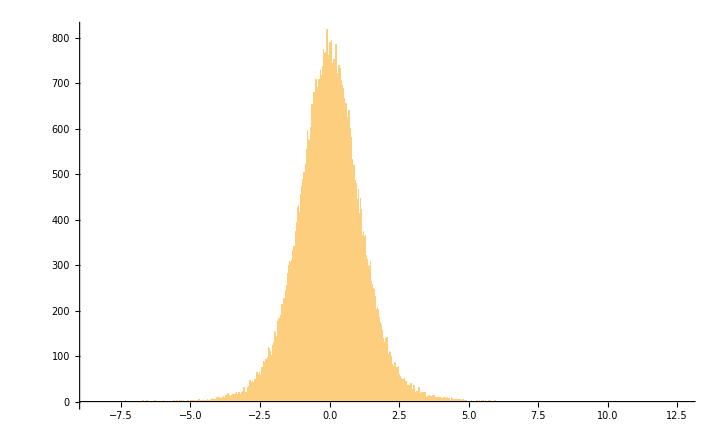

```mathematica
Histogram[studentSampleForMM,1000]
```

```mathematica
MPCSTres9ForMM=MyPearsonChiSquareTest[studentSampleForMM,K,StudentTDistribution[m],ϵ]
```

{0,1055.74,1073.64}

```mathematica
MKTres9ForMM=MyKolmogorovTest[studentSampleForMM,n,StudentTDistribution[m],ΔK]
```

{0,1.0051,1.36}

### Моделирование на основе встроенного программного генератора

```mathematica
studentSampleForInline=StudentCRVGenerator[RandomReal[1,12(m+1)n],n,m];
```

```mathematica
smean9Inline=Mean[studentSampleForInline];Print[{N[mean9],smean9Inline}]
```

{0.,-0.00257979}

```mathematica
svariance9Inline=Variance[studentSampleForInline];Print[{N[variance9], svariance9Inline}]
```

{1.4,1.38161}

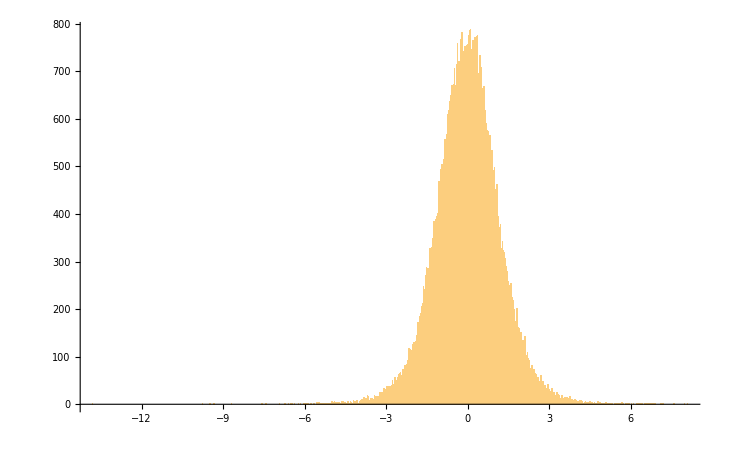

```mathematica
Histogram[studentSampleForInline,1000]
```

```mathematica
MPCSTres9ForInline=MyPearsonChiSquareTest[studentSampleForInline,K,StudentTDistribution[m],ϵ]
```

{0,798.021,1073.64}

```mathematica
MKTres9ForInline=MyKolmogorovTest[studentSampleForInline,n,StudentTDistribution[m],ΔK]
```

{0,1.22886,1.36}

## Моделирование НСВ с распределением хи-квадрат

```mathematica
ChiSquareCRVGenerator[sample_,n_,k_]:=Module[{Z=Table[{NormalCRVGenerator[sample⟦12 (i-1) n+1;;12 i n⟧,n,0,1]},{i,1,k}]},
Return[Flatten[∑_(i=1)^k (Z⟦i⟧)^2]]]
```

```mathematica
k=4;
```

### Моделирование на основе генератора Макларена - Марсальи

```mathematica
chiSquareSampleForMM=ChiSquareCRVGenerator[MMG[paramsMM⟦1;;4⟧,paramsMM⟦5;;8⟧,12k n ,paramsMM⟦9⟧],n,k];
```

```mathematica
mean10=Mean[ChiSquareDistribution[k]];smean10MM=Mean[chiSquareSampleForMM];Print[{N[mean10],smean10MM}]
```

{4.,4.00118608}

```mathematica
variance10=Variance[ChiSquareDistribution[k]];svariance10MM=Variance[chiSquareSampleForMM];Print[{N[variance10], svariance10MM}]
```

{8.,7.5641897}

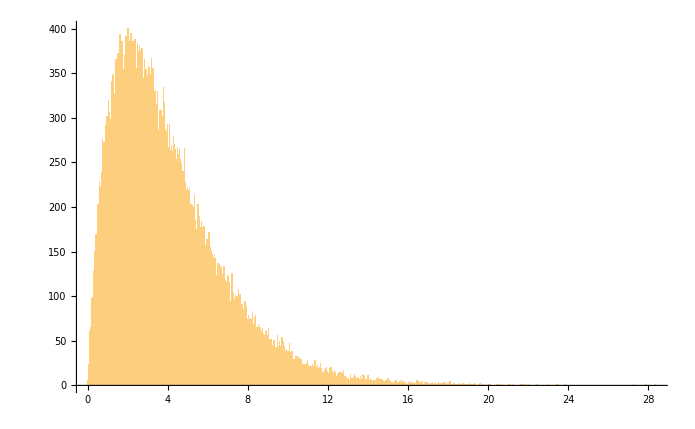

```mathematica
Histogram[chiSquareSampleForMM,1000]
```

```mathematica
MPCSTres10ForMM=MyPearsonChiSquareTest[chiSquareSampleForMM,K,ChiSquareDistribution[k],ϵ]
```

{0,920.149,1073.64}

```mathematica
MKTres10ForMM=MyKolmogorovTest[chiSquareSampleForMM,n,ChiSquareDistribution[k],ΔK]
```

{1,2.77625,1.36}

### Моделирование на основе встроенного программного генератора

```mathematica
chiSquareSampleForInline=ChiSquareCRVGenerator[RandomReal[1,12k n],n,k];
```

```mathematica
smean10Inline=Mean[chiSquareSampleForInline];Print[{N[mean10],smean10Inline}]
```

{4.,3.99813}

```mathematica
svariance10Inline=Variance[chiSquareSampleForInline];Print[{N[variance10], svariance10Inline}]
```

{8.,7.57139}

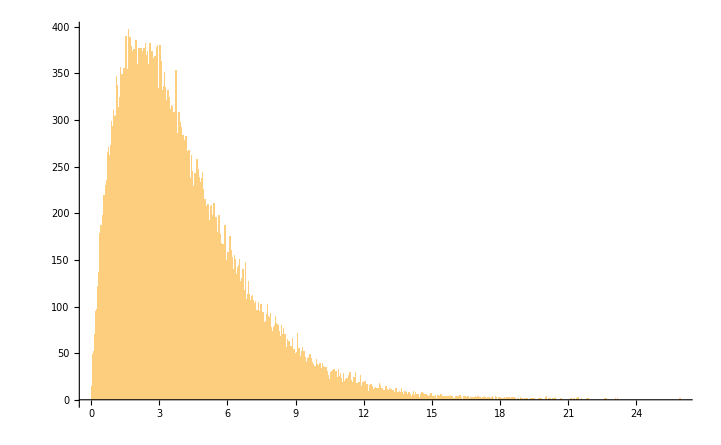

```mathematica
Histogram[chiSquareSampleForInline,1000]
```

```mathematica
MPCSTres10ForInline=MyPearsonChiSquareTest[chiSquareSampleForInline,K,ChiSquareDistribution[k],ϵ]
```

{0,859.044,1073.64}

```mathematica
MKTres10ForInline=MyKolmogorovTest[chiSquareSampleForInline,n,ChiSquareDistribution[k],ΔK]
```

{1,2.47824,1.36}